# Main Biexciton State - Production Plots

Dedicated plotting notebook for the ground exciton X00 and the main biexciton XX0000. It reads the completed seven-geometry refined summary and produces:
(1) E_XX versus c at a = 5 and versus a at c = 1; 
(2) E_bind = 2 E_X - E_XX along the same scans; and 
(3) the radiative lifetimes tau_X and tau_XX. 
Lifetimes follow Eqs. (23)-(25) of Hayrapetyan et al., Physica E 105 (2019) 47-55. The production energies exclude the band gap, so E_exc = E_g + E_X is used in the lifetime formula. Error bars are rough first-order propagation of the stored numerical-integration error estimates.

## Load completed production data

```mathematica
ClearAll["Global`*"];
dir = NotebookDirectory[];
numDir = FileNameJoin[{ParentDirectory[dir], "01-numerics"}];
summaryFile = FileNameJoin[{numDir, "main-state-final-summary-meV.csv"}];

rawTable = Import[summaryFile, "CSV"];
header = First[rawTable];
productionRows = AssociationThread[header, #] & /@ Rest[rawTable];

If[Length[productionRows] =!= 7,
 Print["Expected 7 production rows, found ", Length[productionRows], "."]
 ];

cScanRows = SortBy[
   Select[productionRows, Abs[N[#1["a/rB"]] - 5.] < 10^-8 &],
   #1["c/rB"] &];
aScanRows = SortBy[
   Select[productionRows, Abs[N[#1["c/rB"]] - 1.] < 10^-8 &],
   #1["a/rB"] &];

Dataset[productionRows]
```

## Radiative lifetime model from the reference paper

The reference gives tau_XX approximately tau_X/4 [Eq. (23)], 
tau_X = 2 Pi epsilon_0 m c_light^3 hbar^2/(Sqrt[epsilon] e^2 E_exc^2 f) [Eq. (24)], and f = (E_P/E_exc) |M_X|^2 [Eq. (25)]. Here M_X is the normalized coincidence overlap stored by the production notebook. The GaAs parameters below are taken from Table 1 of the same paper.

```mathematica
(* SI constants *)
vacuumPermittivity = 8.8541878128*^-12;
elementaryCharge = 1.602176634*^-19;
reducedPlanck = 1.054571817*^-34;
speedOfLight = 2.99792458*^8;
freeElectronMass = 9.1093837015*^-31;

(* GaAs parameters from Table 1 of the reference paper. *)
gaasGapEV = 1.5192;
gaasElectronMassRatio = 0.067;
gaasKaneEnergyEV = 22.71;
gaasRelativePermittivity = 12.8;
gaasElectronMass = gaasElectronMassRatio freeElectronMass;

ClearAll[excitonEnergyEV, oscillatorStrengthX, tauXps, tauXXps, tauXErrorPs, tauXXErrorPs];

excitonEnergyEV[row_Association] :=
  gaasGapEV + row["E_X (meV)"]/1000.;

oscillatorStrengthX[row_Association] :=
  (gaasKaneEnergyEV/excitonEnergyEV[row]) row["|M_X|^2"];

tauXps[row_Association] := 10^12 *
  (2 Pi vacuumPermittivity gaasElectronMass speedOfLight^3 reducedPlanck^2)/
   (Sqrt[gaasRelativePermittivity] elementaryCharge^2
     (excitonEnergyEV[row] elementaryCharge)^2 oscillatorStrengthX[row]);

tauXXps[row_Association] := tauXps[row]/4.;

tauXErrorPs[row_Association] := tauXps[row] Norm[{row["E_X error (meV)"]/(1000. excitonEnergyEV[row]), row["|M_X|^2 error"]/row["|M_X|^2"]}];
tauXXErrorPs[row_Association] := tauXErrorPs[row]/4.;

plotRows = Map[
   Join[#1,
     <|"E_exc (eV)" -> excitonEnergyEV[#1],
       "f_X" -> oscillatorStrengthX[#1],
       "tau_X (ps)" -> tauXps[#1],
       "tau_XX (ps)" -> tauXXps[#1],
       "tau_X error (ps)" -> tauXErrorPs[#1],
       "tau_XX error (ps)" -> tauXXErrorPs[#1]|>] &,
   productionRows];

cScan = SortBy[
   Select[plotRows, Abs[N[#1["a/rB"]] - 5.] < 10^-8 &],
   #1["c/rB"] &];
aScan = SortBy[
   Select[plotRows, Abs[N[#1["c/rB"]] - 1.] < 10^-8 &],
   #1["a/rB"] &];

Dataset[KeyTake[#1, {"a/rB", "c/rB", "E_exc (eV)", "M_X", "f_X",
       "tau_X (ps)", "tau_XX (ps)"}] & /@ plotRows]
```

## Shared paper style

```mathematica
ClearAll[paddedRange, panelTag, geometryLabel, quantityLabel, plotErrorKeys, scanPairs];

colors = ColorData[97, "ColorList"];
mainStyle = Directive[colors[[1]], AbsoluteThickness[1.2]];
tauStyles = Thread[Directive[colors[[;; 2]], AbsoluteThickness[1.2]]];
tauGlyph = FromCharacterCode[964];

paddedRange[values_List, fraction_: 0.08] := Module[{lo, hi, pad},
  lo = Min[values]; hi = Max[values];
  pad = If[hi == lo, Max[Abs[lo] fraction, 1.], fraction (hi - lo)];
  {lo - pad, hi + pad}
  ];

panelTag[ch_String] := Row[{Style[ch, Italic], ")"},
  BaseStyle -> {FontFamily -> "Times", FontSize -> 14}];

geometryLabel[s_String] := Row[
  {Style[s, Italic], ", ", Subscript[Style["r", Italic], "B"]},
  BaseStyle -> {FontFamily -> "Times"}];

quantityLabel[s_, unit_String] := Rotate[
  Row[{Style[s, Italic], ", ", unit},
   BaseStyle -> {FontFamily -> "Times"}], -90 Degree];

plotErrorKeys = <|"E_XX (meV)" -> "E_XX error (meV)",
  "E_bind = 2 E_X - E_XX (meV)" -> "E_bind error (meV)",
  "tau_X (ps)" -> "tau_X error (ps)",
  "tau_XX (ps)" -> "tau_XX error (ps)"|>;

SetOptions[ListLinePlot, IntervalMarkers -> "Bars"];

scanPairs[rows_List, xKey_String, yKey_String] :=
  ({#1[xKey], If[KeyExistsQ[plotErrorKeys, yKey], Around[#1[yKey], #1[plotErrorKeys[yKey]]], #1[yKey]]} & /@ rows);
```

## Biexciton energy

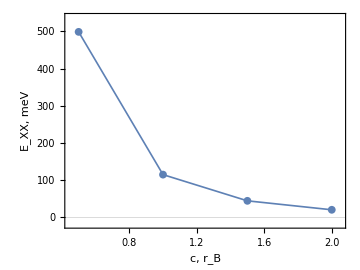
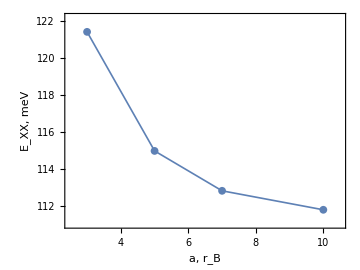
-Graphics- | -Graphics-

```mathematica
eXXc = #1["E_XX (meV)"] & /@ cScan;
eXXa = #1["E_XX (meV)"] & /@ aScan;

plotEXXc = Labeled[
  ListLinePlot[scanPairs[cScan, "c/rB", "E_XX (meV)"],
   Joined -> True,
   PlotStyle -> mainStyle,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["c"],
     quantityLabel[Subscript["E", "XX"], "meV"]},
   PlotRange -> {{0.45, 2.05}, paddedRange[eXXc]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["a"], {Left, Top}, Spacings -> {0, 0}];

plotEXXa = Labeled[
  ListLinePlot[scanPairs[aScan, "a/rB", "E_XX (meV)"],
   Joined -> True,
   PlotStyle -> mainStyle,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["a"],
     quantityLabel[Subscript["E", "XX"], "meV"]},
   PlotRange -> {{2.5, 10.5}, paddedRange[eXXa]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["b"], {Left, Top}, Spacings -> {0, 0}];

figEXX = Grid[{{plotEXXc, plotEXXa}}, Spacings -> {0, 0},
  Alignment -> Top];
figEXX
```

## Biexciton binding energy

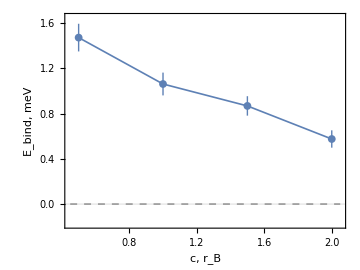
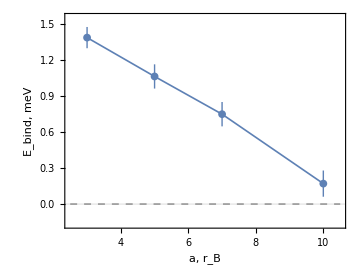
-Graphics- | -Graphics-

```mathematica
bindC = #1["E_bind = 2 E_X - E_XX (meV)"] & /@ cScan;
bindA = #1["E_bind = 2 E_X - E_XX (meV)"] & /@ aScan;
bindRangeC = paddedRange[Join[bindC, {0.}], 0.12];
bindRangeA = paddedRange[Join[bindA, {0.}], 0.12];

plotBindC = Labeled[
  ListLinePlot[
   scanPairs[cScan, "c/rB", "E_bind = 2 E_X - E_XX (meV)"],
   Joined -> True,
   PlotStyle -> mainStyle,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["c"],
     quantityLabel[Subscript["E", "bind"], "meV"]},
   PlotRange -> {{0.45, 2.05}, bindRangeC},
   Epilog -> {Directive[GrayLevel[0.55], Dashed],
     Line[{{0.45, 0}, {2.05, 0}}]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["a"], {Left, Top}, Spacings -> {0, 0}];

plotBindA = Labeled[
  ListLinePlot[
   scanPairs[aScan, "a/rB", "E_bind = 2 E_X - E_XX (meV)"],
   Joined -> True,
   PlotStyle -> mainStyle,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["a"],
     quantityLabel[Subscript["E", "bind"], "meV"]},
   PlotRange -> {{2.5, 10.5}, bindRangeA},
   Epilog -> {Directive[GrayLevel[0.55], Dashed],
     Line[{{2.5, 0}, {10.5, 0}}]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["b"], {Left, Top}, Spacings -> {0, 0}];

figBinding = Grid[{{plotBindC, plotBindA}}, Spacings -> {0, 0},
  Alignment -> Top];
figBinding
```

## Exciton and biexciton lifetimes

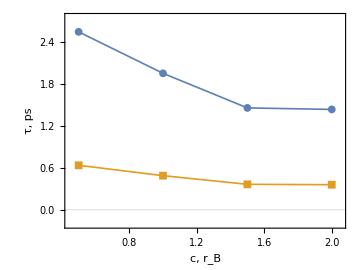
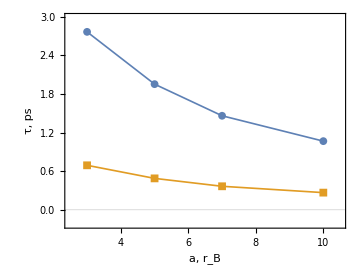
-Graphics- | -Graphics-

```mathematica
tauC = Join[#1["tau_X (ps)"] & /@ cScan,
   #1["tau_XX (ps)"] & /@ cScan];
tauA = Join[#1["tau_X (ps)"] & /@ aScan,
   #1["tau_XX (ps)"] & /@ aScan];

tauLegend = LineLegend[tauStyles,
  {Style[Subscript[tauGlyph, "X"], Italic],
   Style[Subscript[tauGlyph, "XX"], Italic]},
  LabelStyle -> {FontFamily -> "Times", FontSize -> 11},
  LegendLayout -> "Row"];

plotTauC = Labeled[
  ListLinePlot[{
    scanPairs[cScan, "c/rB", "tau_X (ps)"],
    scanPairs[cScan, "c/rB", "tau_XX (ps)"]},
   Joined -> True,
   PlotStyle -> tauStyles,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["c"], quantityLabel[tauGlyph, "ps"]},
   PlotRange -> {{0.45, 2.05}, paddedRange[Join[tauC, {0.}]]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["a"], {Left, Top}, Spacings -> {0, 0}];

plotTauA = Labeled[
  ListLinePlot[{
    scanPairs[aScan, "a/rB", "tau_X (ps)"],
    scanPairs[aScan, "a/rB", "tau_XX (ps)"]},
   Joined -> True,
   PlotStyle -> tauStyles,
   PlotMarkers -> {Automatic, 8},
   PlotTheme -> "Scientific",
   Frame -> True,
   FrameLabel -> {geometryLabel["a"], quantityLabel[tauGlyph, "ps"]},
   PlotRange -> {{2.5, 10.5}, paddedRange[Join[tauA, {0.}]]},
   BaseStyle -> {FontFamily -> "Times"},
   ImagePadding -> {{65, 15}, {50, 15}},
   AspectRatio -> 0.75,
   ImageSize -> 360],
  panelTag["b"], {Left, Top}, Spacings -> {0, 0}];

figLifetimes = Column[
  {Grid[{{plotTauC, plotTauA}}, Spacings -> {0, 0}, Alignment -> Top],
   tauLegend}, Alignment -> Center, Spacings -> 0.2];
figLifetimes
```

## Export manuscript figures

```mathematica
Export[FileNameJoin[{dir, "Main-E_XX.pdf"}], figEXX];
Export[FileNameJoin[{dir, "Main-Binding-Energy.pdf"}], figBinding];
Export[FileNameJoin[{dir, "Main-Lifetimes.pdf"}], figLifetimes];

Column[FileNames["Main-*.pdf", dir]]
```

C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\Main-Binding-Energy.pdf
C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\Main-E_XX.pdf
C:\Users\davit\Documents\PhD\projects\biexciton\03-figures\Main-Lifetimes.pdf